```mathematica
Clear[λ0,δλ,β]
λ[t_]=λ0+δλ t/τ;
H[q_,p_,t_]=p^2/2+λ[t]q^2/2;

sol=FullSimplify[DSolve[{q'[t]== p[t],p'[t]== -λ[t]q[t],q[0]==q0,p[0]==p0},{q[t],p[t]},t]];

q1[t_]=q[t]/.sol[[1,2]];
p1[t_]=p[t]/.sol[[1,1]];
```

0.25

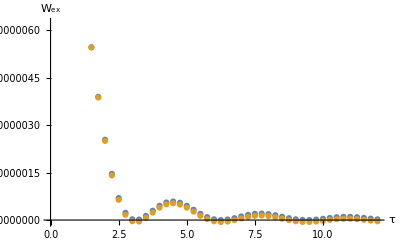

```mathematica
Clear[λ0,δλ,β]

δλ=0.01;
β=1;
λ0=1;

(* EXCESS WORK *)

W[q0_,p0_]=Expand[H[q1[τ],p1[τ],τ]-H[q1[0],p1[0],0]];

partition=Assuming[{β>0,λ0>0},Integrate[Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]];
a1=Assuming[{β>0,λ0>0},Integrate[q0 p0 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a2=Assuming[{β>0,λ0>0},Integrate[q0^2 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a3=Assuming[{β>0,λ0>0},Integrate[p0^2 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;

Wm[τ_]=Expand[W[q0,p0]]/.{p0 q0-> a1,p0 π^2 q0->π^2 a1,p0 π q0->π a1,q0^2-> a2,p0^2-> a3};
Wex[τ_]=Wm[τ]-(√(1+δλ/λ0)-1)/β;

data1=Table[{τ,Wex[τ]},{τ,0.001,12.1,0.25}];

(* VARIANCE OF WORK *)

W21[q0_,p0_]=Expand[(W[q0,p0]-Wm[τ])^2];

a4=Assuming[{β>0,λ0>0},Integrate[p0^4 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a5=Assuming[{β>0,λ0>0},Integrate[q0^4 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a6=Assuming[{β>0,λ0>0},Integrate[p0^2q0^2 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a7=Assuming[{β>0,λ0>0},Integrate[p0^3q0 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a8=Assuming[{β>0,λ0>0},Integrate[p0 q0^3 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;

varW[τ_]=Expand[W21[q0,p0]]/.{p0 q0-> a1,p0 π^2 q0->π^2 a1,p0 π q0->π a1,q0^2-> a2,p0^2-> a3,p0^4-> a4,q0^4-> a5,p0^2 π^4 q0^2->a6 π^4,p0^3 π^4 q0-> a7 π^4,p0^3 q0-> a7 ,p0 π^4 q0^3-> a8 π^4,p0 q0^3-> a8 ,p0^2 π^3 q0^2->a6 π^3,p0^2 q0^2->a6,p0^3 π^3 q0-> a7 π^3,p0 π^3 q0^3-> a8 π^3};

varWqs=1/8(a5-a2^2)

data2=Table[{τ,varW[τ]/2-(δλ^2 varWqs)/2},{τ,0.001,12.1,0.25}];

plotWex=ListPlot[{data1,data2},AxesLabel->{"τ","W_ex"}]

Export["Research/ongoing/VTILR/data/dataWex.dat",data1];
Export["Research/ongoing/VTILR/data/dataVar.dat",data2];
```

Optimal variance and optimal work distribution

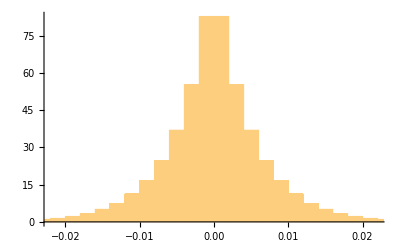

```mathematica
Clear[n,λ0,δλ,β,qi,pi];

n=100000;

β=1;
λ0=1;
δλ=0.01;

(*data4=List[];*)

Do[

qi=RandomVariate[NormalDistribution[0,1/(β λ0)]];
pi=RandomVariate[NormalDistribution[0,1/β ]];

Wqs=(δλ/(2 λ0) -1/8(δλ/λ0)^2)(pi^2/2+(qi^2 λ0)/2);

data4=AppendTo[data4,Wqs];

,{i,1,n}];

Histogram[data4,Automatic,"PDF"]
```

```mathematica
Mean[data4]
Variance[data4]
Cumulant[data4,3]
Cumulant[data4,4]
Cumulant[data4,5]
```

0.

0.0000497463

0.

7.54611×10^-9

0.